{a1→-4.1328,b1→0.0244683,k1→6.69375,a2→3.892,b2→0.0225652,k2→6.36808,c→8.91484}

8.0248

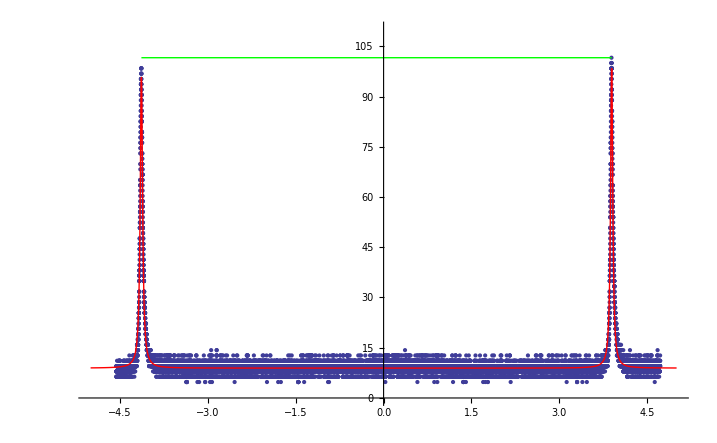

```mathematica
rawData = Import[NotebookDirectory[]<>"kalibrierung_modenabstand.dat"];
messData = ToExpression[rawData];
messData = Take[messData, {17000, 46000}];
Second[x_] := x[[2]];
timeData = Map[First, messData];
sensorData =  Flatten[Map[Second, messData]];
rechteckData = Map[Last, messData];
sensorData = Table[{timeData[[k]],sensorData[[k]]},{k,1,Length[timeData]}];
rechteckData = Table[{timeData[[k]],rechteckData[[k]]},{k,1,Length[timeData]}];
Clear @ model;
model[x_] =k1/((1+(x-a1)^2/b1^2) b1 π)+k2/((1+(x-a2)^2/b2^2) b2 π) +c;
param=FindFit[sensorData, model[x], {{a1,-4},{ b1,0.1},{  k1, 18},{ a2,4},{  b2,0.1},{  k2,18},{  c,10}}, x]
Distance = a2-a1 /. param
Peak = Max[sensorData];
Show[ListPlot[sensorData, PlotRange->{{-5, 5},{0,  110}}], Plot[model[x]  /. param, {x, -5, 5}, PlotRange->{{-5, 5},{0, 110}}, PlotStyle->Red], Graphics[{Green, Line[{{a1,Peak},{a2,Peak}} /. param]}]]
```